## Build Covariance Matrix

```mathematica
M = {{-(2*κ+k)/γ,0},{δ*κ/γ,-k/γ}};
```

```mathematica
MatrixForm[M]
```

((-k-2 κ)/γ | 0
(δ κ)/γ | -k/γ)

```mathematica
expM = MatrixExp[M*(t-tp)];
```

```mathematica
cov = Integrate[expM.{{4*T/γ,0},{0,T/(γ)*(1-δ^2)}}.Transpose[expM],{tp,-∞,t},Assumptions->{γ>0,k>0,κ>0}]
```

{{(2 T)/(k+2 κ),(T δ κ)/((k+κ) (k+2 κ))},{(T δ κ)/((k+κ) (k+2 κ)),1/2 T (1/k+δ^2 (-2/(k+κ)+1/(k+2 κ)))}}

```mathematica
cov = Simplify[cov]
```

{{(2 T)/(k+2 κ),(T δ κ)/((k+κ) (k+2 κ))},{(T δ κ)/((k+κ) (k+2 κ)),1/2 T (1/k+δ^2 (-2/(k+κ)+1/(k+2 κ)))}}

```mathematica
P[R_,r_,kk_] := Simplify[Exp[-1/2*{r,R}.Inverse[cov].{r,R}]]/.{k-> kk}
```

```mathematica
P[1,1,1]
```

ⅇ^(-((1+κ) (-5+δ^2+(-7+4 δ+3 δ^2) κ-2 κ^2))/(4 T (-1+δ^2+2 (-1+δ^2) κ-κ^2)))

## Patching and Normalisation

```mathematica
SubMinus[k]=2*Subscript[u, 0]/(L^2)
```

(2 u_0)/L^2

```mathematica
SubPlus[k]= 2*Subscript[u, 0]/(l^2)
```

(2 u_0)/l^2

```mathematica
SubMinus[f]= Simplify[Integrate[P[R,r,SubMinus[k]],{r,-∞,∞},Assumptions->{Subscript[u, 0]>0,κ>0,γ>0,L>0,l>0,δ<1,δ>0,SubMinus[k]>0,T>0}],Assumptions->{Subscript[u, 0]>0,κ>0,γ>0,L>0,l>0,δ<1,δ>0,SubMinus[k]>0,T>0}]
```

-(ⅇ^(-(2 R^2 u_0 (L^2 κ+u_0) (L^2 κ+2 u_0))/(L^2 T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2))) L √(2 π) √((T (L^8 κ^4-7 L^6 (-1+δ^2) κ^3 u_0+6 L^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 L^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(L^2 κ+2 u_0)))/(-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2)

```mathematica
SubPlus[f]= Simplify[Integrate[P[R,r,SubPlus[k]],{r,-∞,∞},Assumptions->{Subscript[u, 0]>0,κ>0,γ>0,l>0,δ<1,δ>0,SubPlus[k]>0,T>0}],Assumptions->{Subscript[u, 0]>0,κ>0,γ>0,l>0,δ<1,δ>0,SubPlus[k]>0,T>0}]
```

-(ⅇ^(-(2 R^2 u_0 (l^2 κ+u_0) (l^2 κ+2 u_0))/(l^2 T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2))) l √(2 π) √((T (l^8 κ^4-7 l^6 (-1+δ^2) κ^3 u_0+6 l^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 l^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(l^2 κ+2 u_0)))/(-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2)

```mathematica
SubMinus[int] = Simplify[Integrate[SubMinus[f],{R,-L,0},Assumptions->{Subscript[u, 0]>0,κ>0,γ>0,L>0,δ<1,δ>0,SubMinus[k]>0,T>0}]]
```

(L^2 π T Erf[√2 √((u_0 (L^4 κ^2+3 L^2 κ u_0+2 u_0^2))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))])/(2 (L^2 κ+2 u_0) √(-(u_0 (L^2 κ+u_0))/(-L^4 κ^2+4 L^2 (-1+δ^2) κ u_0+4 (-1+δ^2) u_0^2)))

```mathematica
SubPlus[int] = Simplify[Integrate[SubPlus[f],{R,0,l},Assumptions->{Subscript[u, 0]>0,κ>0,γ>0,l>0,δ<1,δ>0,SubPlus[k]>0,T>0}]]
```

(l^2 π T Erf[√2 √((u_0 (l^4 κ^2+3 l^2 κ u_0+2 u_0^2))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))])/(2 (l^2 κ+2 u_0) √(-(u_0 (l^2 κ+u_0))/(-l^4 κ^2+4 l^2 (-1+δ^2) κ u_0+4 (-1+δ^2) u_0^2)))

```mathematica
{{SubMinus[exprA],SubPlus[exprA]}}=Simplify[Solve[SubMinus[A]*(SubMinus[f]/.{R-> 0})==SubPlus[A]*(SubPlus[f]/.{R-> 0}) && SubMinus[A]*SubMinus[int]+SubPlus[A]*SubPlus[int]==1,{SubMinus[A],SubPlus[A]}],Assumptions->{Subscript[u, 0]>0,κ>0,γ>0,L>0,0<δ<1,T>0,l>0}]
```

{{A_-→(2 √((T (l^8 κ^4-7 l^6 (-1+δ^2) κ^3 u_0+6 l^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 l^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(l^2 κ+2 u_0)))/(L π T (-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2) ((L Erf[√2 √((u_0 (L^4 κ^2+3 L^2 κ u_0+2 u_0^2))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √((T (L^4 κ^2-4 L^2 (-1+δ^2) κ u_0-4 (-1+δ^2) u_0^2) (l^8 κ^4-7 l^6 (-1+δ^2) κ^3 u_0+6 l^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 l^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(u_0 (L^2 κ+u_0) (l^2 κ+2 u_0))))/((L^2 κ+2 u_0) (-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))+(l Erf[√2 √((u_0 (l^4 κ^2+3 l^2 κ u_0+2 u_0^2))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √((T (l^4 κ^2-4 l^2 (-1+δ^2) κ u_0-4 (-1+δ^2) u_0^2) (L^8 κ^4-7 L^6 (-1+δ^2) κ^3 u_0+6 L^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 L^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(u_0 (l^2 κ+u_0) (L^2 κ+2 u_0))))/((l^2 κ+2 u_0) (-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2)))),A_+→-((2 u_0 (l^2 κ+2 u_0) (-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2) √((T (l^2 κ+u_0) (L^2 κ+u_0) (L^2 κ+2 u_0) (-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))/(-l^4 κ^2+4 l^2 (-1+δ^2) κ u_0+4 (-1+δ^2) u_0^2)))/(l π T (-4 (-1+δ^2) u_0^3 (L Erf[√2 √((u_0 (L^4 κ^2+3 L^2 κ u_0+2 u_0^2))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √(-(T u_0 (l^2 κ+u_0) (-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))/(l^2 κ+2 u_0))+l Erf[√2 √((u_0 (l^4 κ^2+3 l^2 κ u_0+2 u_0^2))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √(-(T u_0 (L^2 κ+u_0) (-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))/(L^2 κ+2 u_0)))+l^2 L^2 κ^3 (L^3 Erf[√2 √((u_0 (L^4 κ^2+3 L^2 κ u_0+2 u_0^2))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √(-(T u_0 (l^2 κ+u_0) (-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))/(l^2 κ+2 u_0))+l^3 Erf[√2 √((u_0 (l^4 κ^2+3 l^2 κ u_0+2 u_0^2))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √(-(T u_0 (L^2 κ+u_0) (-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))/(L^2 κ+2 u_0)))-2 (-1+δ^2) κ u_0^2 (L (l^2+3 L^2) Erf[√2 √((u_0 (L^4 κ^2+3 L^2 κ u_0+2 u_0^2))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √(-(T u_0 (l^2 κ+u_0) (-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))/(l^2 κ+2 u_0))+l (3 l^2+L^2) Erf[√2 √((u_0 (l^4 κ^2+3 l^2 κ u_0+2 u_0^2))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √(-(T u_0 (L^2 κ+u_0) (-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))/(L^2 κ+2 u_0)))+κ^2 u_0 (L^3 (2 L^2-3 l^2 (-1+δ^2)) Erf[√2 √((u_0 (L^4 κ^2+3 L^2 κ u_0+2 u_0^2))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √(-(T u_0 (l^2 κ+u_0) (-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))/(l^2 κ+2 u_0))+l^3 (2 l^2-3 L^2 (-1+δ^2)) Erf[√2 √((u_0 (l^4 κ^2+3 l^2 κ u_0+2 u_0^2))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √(-(T u_0 (L^2 κ+u_0) (-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))/(L^2 κ+2 u_0))))))}}

```mathematica
SubMinus[exprA]=SubMinus[A]->Simplify[(SubPlus[f]/(SubMinus[f]*SubPlus[int]+SubPlus[f]*SubMinus[int]))/.{R->0}]
```

A_-→(l √(2 π) √((T (l^8 κ^4-7 l^6 (-1+δ^2) κ^3 u_0+6 l^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 l^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(l^2 κ+2 u_0)))/((-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2) ((l L^2 π^(3/2) T Erf[√2 √((u_0 (L^4 κ^2+3 L^2 κ u_0+2 u_0^2))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √((T (l^8 κ^4-7 l^6 (-1+δ^2) κ^3 u_0+6 l^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 l^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(l^2 κ+2 u_0)))/(√2 (L^2 κ+2 u_0) (-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2) √(-(u_0 (L^2 κ+u_0))/(-L^4 κ^2+4 L^2 (-1+δ^2) κ u_0+4 (-1+δ^2) u_0^2)))+(l^2 L π^(3/2) T Erf[√2 √((u_0 (l^4 κ^2+3 l^2 κ u_0+2 u_0^2))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √((T (L^8 κ^4-7 L^6 (-1+δ^2) κ^3 u_0+6 L^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 L^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(L^2 κ+2 u_0)))/(√2 (l^2 κ+2 u_0) (-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2) √(-(u_0 (l^2 κ+u_0))/(-l^4 κ^2+4 l^2 (-1+δ^2) κ u_0+4 (-1+δ^2) u_0^2)))))

```mathematica
SubPlus[exprA]=SubPlus[A]->Simplify[(SubMinus[f]/(SubMinus[f]*SubPlus[int]+SubPlus[f]*SubMinus[int]))/.{R->0}]
```

A_+→(L √(2 π) √((T (L^8 κ^4-7 L^6 (-1+δ^2) κ^3 u_0+6 L^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 L^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(L^2 κ+2 u_0)))/((-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2) ((l L^2 π^(3/2) T Erf[√2 √((u_0 (L^4 κ^2+3 L^2 κ u_0+2 u_0^2))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √((T (l^8 κ^4-7 l^6 (-1+δ^2) κ^3 u_0+6 l^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 l^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(l^2 κ+2 u_0)))/(√2 (L^2 κ+2 u_0) (-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2) √(-(u_0 (L^2 κ+u_0))/(-L^4 κ^2+4 L^2 (-1+δ^2) κ u_0+4 (-1+δ^2) u_0^2)))+(l^2 L π^(3/2) T Erf[√2 √((u_0 (l^4 κ^2+3 l^2 κ u_0+2 u_0^2))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √((T (L^8 κ^4-7 L^6 (-1+δ^2) κ^3 u_0+6 L^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 L^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(L^2 κ+2 u_0)))/(√2 (l^2 κ+2 u_0) (-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2) √(-(u_0 (l^2 κ+u_0))/(-l^4 κ^2+4 l^2 (-1+δ^2) κ u_0+4 (-1+δ^2) u_0^2)))))

## Current

```mathematica
Subscript[J, R]= Simplify[-k*R/γ*P[R,r,k]+δ*κ*r/γ*P[R,r,k]-T*(1-δ^2)/(2*γ)*D[P[R,r,k],R]]
```

(ⅇ^(-((k+κ) (k^2 (-4 R^2+r^2 (-1+δ^2))+k (-4 R^2+4 r R δ+3 r^2 (-1+δ^2)) κ-2 r^2 κ^2))/(4 T (k^2 (-1+δ^2)+2 k (-1+δ^2) κ-κ^2))) δ κ (k^2 (r-r δ^2)+k (-2 R δ-3 r (-1+δ^2)) κ+2 r κ^2))/(2 γ (-k^2 (-1+δ^2)-2 k (-1+δ^2) κ+κ^2))

```mathematica
{{SubMinus[exprr]}}= FullSimplify[Solve[(Subscript[J, R]/P[R,r,k]/.{R->- L,k-> SubMinus[k]})==0,r],Assumptions->{Subscript[u, 0]>0,κ>0,γ>0,L>0,δ<1,δ>0,SubMinus[k]>0,T>0}]
```

{{r→-(2 L^3 δ κ u_0)/(L^4 κ^2-(-1+δ^2) u_0 (3 L^2 κ+2 u_0))}}

```mathematica
{{SubPlus[exprr]}}= FullSimplify[Solve[(Subscript[J, R]/P[R,r,k]/.{R-> l,k-> SubPlus[k]})==0,r],Assumptions->{Subscript[u, 0]>0,κ>0,γ>0,l>0,δ<1,δ>0,SubPlus[k]>0,T>0}]
```

{{r→(2 l^3 δ κ u_0)/(l^4 κ^2-(-1+δ^2) u_0 (3 l^2 κ+2 u_0))}}

```mathematica
Subscript[J, left]=Integrate[SubMinus[A]*Subscript[J, R]/.{R-> -L,k-> SubMinus[k],SubMinus[exprA]},{r,-∞,r/. SubMinus[exprr]},Assumptions->{Subscript[u, 0]>0,κ>0,γ>0,L>0,l>0,δ<1,δ>0,SubMinus[k]>0,T>0}]
```

-((ⅇ^(-(2 u_0 (L^2 κ+u_0) (L^2 κ+2 u_0))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2))) l √(2 π) T δ κ (L^4 κ^2-4 L^2 (-1+δ^2) κ u_0-4 (-1+δ^2) u_0^2) √((T (l^8 κ^4-7 l^6 (-1+δ^2) κ^3 u_0+6 l^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 l^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(l^2 κ+2 u_0)))/(L^2 γ (L^2 κ+2 u_0) (-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2) (κ^2-(4 (-1+δ^2) κ u_0)/L^2-(4 (-1+δ^2) u_0^2)/L^4) ((l L^2 π^(3/2) T Erf[√2 √((u_0 (L^4 κ^2+3 L^2 κ u_0+2 u_0^2))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √(-(T (-L^4 κ^2+4 L^2 (-1+δ^2) κ u_0+4 (-1+δ^2) u_0^2) (l^8 κ^4-7 l^6 (-1+δ^2) κ^3 u_0+6 l^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 l^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(u_0 (L^2 κ+u_0) (l^2 κ+2 u_0))))/(√2 (L^2 κ+2 u_0) (-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))+(l^2 L π^(3/2) T Erf[√2 √((u_0 (l^4 κ^2+3 l^2 κ u_0+2 u_0^2))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √(-(T (-l^4 κ^2+4 l^2 (-1+δ^2) κ u_0+4 (-1+δ^2) u_0^2) (L^8 κ^4-7 L^6 (-1+δ^2) κ^3 u_0+6 L^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 L^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(u_0 (l^2 κ+u_0) (L^2 κ+2 u_0))))/(√2 (l^2 κ+2 u_0) (-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2)))))

```mathematica
Subscript[J, right]=Integrate[SubPlus[A]*Subscript[J, R]/.{R-> l,k-> SubPlus[k],SubPlus[exprA]},{r,r/.{SubPlus[exprr]},Infinity},Assumptions->{Subscript[u, 0]>0,κ>0,γ>0,L>0,l>0,δ<1,δ>0,SubPlus[k]>0,T>0}]
```

(ⅇ^(-(2 u_0 (l^2 κ+u_0) (l^2 κ+2 u_0))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2))) L √(2 π) T δ κ (l^4 κ^2-4 l^2 (-1+δ^2) κ u_0-4 (-1+δ^2) u_0^2) √((T (L^8 κ^4-7 L^6 (-1+δ^2) κ^3 u_0+6 L^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 L^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(L^2 κ+2 u_0)))/(l^2 γ (l^2 κ+2 u_0) (-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2) (κ^2-(4 (-1+δ^2) κ u_0)/l^2-(4 (-1+δ^2) u_0^2)/l^4) ((l L^2 π^(3/2) T Erf[√2 √((u_0 (L^4 κ^2+3 L^2 κ u_0+2 u_0^2))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √(-(T (-L^4 κ^2+4 L^2 (-1+δ^2) κ u_0+4 (-1+δ^2) u_0^2) (l^8 κ^4-7 l^6 (-1+δ^2) κ^3 u_0+6 l^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 l^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(u_0 (L^2 κ+u_0) (l^2 κ+2 u_0))))/(√2 (L^2 κ+2 u_0) (-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))+(l^2 L π^(3/2) T Erf[√2 √((u_0 (l^4 κ^2+3 l^2 κ u_0+2 u_0^2))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √(-(T (-l^4 κ^2+4 l^2 (-1+δ^2) κ u_0+4 (-1+δ^2) u_0^2) (L^8 κ^4-7 L^6 (-1+δ^2) κ^3 u_0+6 L^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 L^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(u_0 (l^2 κ+u_0) (L^2 κ+2 u_0))))/(√2 (l^2 κ+2 u_0) (-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))))

```mathematica
Subscript[J, total]= Simplify[Subscript[J, left]+ Subscript[J, right],Assumptions->{Subscript[u, 0]>0,κ>0,γ>0,L>0,δ<1,δ>0,SubMinus[k]>0,T>0,l>0,SubPlus[k]>0}]
```

-((2 δ κ (-((ⅇ^(-(2 u_0 (L^2 κ+u_0) (L^2 κ+2 u_0))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2))) L √((T (l^8 κ^4-7 l^6 (-1+δ^2) κ^3 u_0+6 l^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 l^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(l^2 κ+2 u_0)))/((L^2 κ+2 u_0) (-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2)))+(ⅇ^(-(2 u_0 (l^2 κ+u_0) (l^2 κ+2 u_0))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2))) l √((T (L^8 κ^4-7 L^6 (-1+δ^2) κ^3 u_0+6 L^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 L^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(L^2 κ+2 u_0)))/((l^2 κ+2 u_0) (-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))))/(π γ ((L Erf[√2 √((u_0 (L^4 κ^2+3 L^2 κ u_0+2 u_0^2))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √((T (L^4 κ^2-4 L^2 (-1+δ^2) κ u_0-4 (-1+δ^2) u_0^2) (l^8 κ^4-7 l^6 (-1+δ^2) κ^3 u_0+6 l^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 l^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(u_0 (L^2 κ+u_0) (l^2 κ+2 u_0))))/((L^2 κ+2 u_0) (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2))+(l Erf[√2 √((u_0 (l^4 κ^2+3 l^2 κ u_0+2 u_0^2))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √((T (l^4 κ^2-4 l^2 (-1+δ^2) κ u_0-4 (-1+δ^2) u_0^2) (L^8 κ^4-7 L^6 (-1+δ^2) κ^3 u_0+6 L^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 L^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(u_0 (l^2 κ+u_0) (L^2 κ+2 u_0))))/((l^2 κ+2 u_0) (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))))

```mathematica
Subscript[J, total]=-((2 δ κ (-((ⅇ^(-(2 Subscript[u, 0] (L^2 κ+Subscript[u, 0]) (L^2 κ+2 Subscript[u, 0]))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ Subscript[u, 0]-2 (-1+δ^2) Subscript[u, 0]^2))) L √((T (l^8 κ^4-7 l^6 (-1+δ^2) κ^3 Subscript[u, 0]+6 l^4 (3-5 δ^2+2 δ^4) κ^2 Subscript[u, 0]^2+20 l^2 (-1+δ^2)^2 κ Subscript[u, 0]^3+8 (-1+δ^2)^2 Subscript[u, 0]^4))/(l^2 κ+2 Subscript[u, 0])))/((L^2 κ+2 Subscript[u, 0]) (-l^4 κ^2+3 l^2 (-1+δ^2) κ Subscript[u, 0]+2 (-1+δ^2) Subscript[u, 0]^2)))+(ⅇ^(-(2 Subscript[u, 0] (l^2 κ+Subscript[u, 0]) (l^2 κ+2 Subscript[u, 0]))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ Subscript[u, 0]-2 (-1+δ^2) Subscript[u, 0]^2))) l √((T (L^8 κ^4-7 L^6 (-1+δ^2) κ^3 Subscript[u, 0]+6 L^4 (3-5 δ^2+2 δ^4) κ^2 Subscript[u, 0]^2+20 L^2 (-1+δ^2)^2 κ Subscript[u, 0]^3+8 (-1+δ^2)^2 Subscript[u, 0]^4))/(L^2 κ+2 Subscript[u, 0])))/((l^2 κ+2 Subscript[u, 0]) (-L^4 κ^2+3 L^2 (-1+δ^2) κ Subscript[u, 0]+2 (-1+δ^2) Subscript[u, 0]^2))))/(π γ ((L Erf[√2 √((Subscript[u, 0] (L^4 κ^2+3 L^2 κ Subscript[u, 0]+2 Subscript[u, 0]^2))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ Subscript[u, 0]-2 (-1+δ^2) Subscript[u, 0]^2)))] √((T (L^4 κ^2-4 L^2 (-1+δ^2) κ Subscript[u, 0]-4 (-1+δ^2) Subscript[u, 0]^2) (l^8 κ^4-7 l^6 (-1+δ^2) κ^3 Subscript[u, 0]+6 l^4 (3-5 δ^2+2 δ^4) κ^2 Subscript[u, 0]^2+20 l^2 (-1+δ^2)^2 κ Subscript[u, 0]^3+8 (-1+δ^2)^2 Subscript[u, 0]^4))/(Subscript[u, 0] (L^2 κ+Subscript[u, 0]) (l^2 κ+2 Subscript[u, 0]))))/((L^2 κ+2 Subscript[u, 0]) (l^4 κ^2-3 l^2 (-1+δ^2) κ Subscript[u, 0]-2 (-1+δ^2) Subscript[u, 0]^2))+(l Erf[√2 √((Subscript[u, 0] (l^4 κ^2+3 l^2 κ Subscript[u, 0]+2 Subscript[u, 0]^2))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ Subscript[u, 0]-2 (-1+δ^2) Subscript[u, 0]^2)))] √((T (l^4 κ^2-4 l^2 (-1+δ^2) κ Subscript[u, 0]-4 (-1+δ^2) Subscript[u, 0]^2) (L^8 κ^4-7 L^6 (-1+δ^2) κ^3 Subscript[u, 0]+6 L^4 (3-5 δ^2+2 δ^4) κ^2 Subscript[u, 0]^2+20 L^2 (-1+δ^2)^2 κ Subscript[u, 0]^3+8 (-1+δ^2)^2 Subscript[u, 0]^4))/(Subscript[u, 0] (l^2 κ+Subscript[u, 0]) (L^2 κ+2 Subscript[u, 0]))))/((l^2 κ+2 Subscript[u, 0]) (L^4 κ^2-3 L^2 (-1+δ^2) κ Subscript[u, 0]-2 (-1+δ^2) Subscript[u, 0]^2)))));
```

```mathematica
Subscript[J, simp]= FullSimplify[Subscript[J, total]/.{γ->0.01,Subscript[u, 0]->1,l->9.0,L->1.0,δ->(-Subscript[T, 1]+Subscript[T, 2])/(Subscript[T, 1]+Subscript[T, 2]),T->(Subscript[T, 1]+Subscript[T, 2])/2},{Subscript[T, 2]>Subscript[T, 1]>0}]
```

-((63.662 κ (-T_1+T_2) ((0.0785674 ⅇ^(-(4. (1.+1. κ) (2.+1. κ) (T_1+T_2))/(1. κ^2 T_1^2+(8.+κ (12.+2. κ)) T_1 T_2+1. κ^2 T_2^2)) √(1/(0.0246914+1. κ)(T_1+T_2) (1. κ^4 T_1^4+κ^2 (0.00365798+κ (0.345679+4. κ)) T_1^3 T_2+(2.97351×10^-6+κ (0.000602136+κ (0.0365798+κ (0.691358+6. κ)))) T_1^2 T_2^2+κ^2 (0.00365798+κ (0.345679+4. κ)) T_1 T_2^3+1. κ^4 T_2^4)))/((2.+1. κ) (1. κ^2 T_1^2+(0.00121933+κ (0.148148+2. κ)) T_1 T_2+1. κ^2 T_2^2))-(0.0785674 ⅇ^(-(4. (0.0123457+1. κ) (0.0246914+1. κ) (T_1+T_2))/(1. κ^2 T_1^2+(0.00121933+κ (0.148148+2. κ)) T_1 T_2+1. κ^2 T_2^2)) √(1/(2.+1. κ)(T_1+T_2) (1. κ^4 T_1^4+κ^2 (24.+κ (28.+4. κ)) T_1^3 T_2+(128.+κ (320.+κ (240.+κ (56.+6. κ)))) T_1^2 T_2^2+κ^2 (24.+κ (28.+4. κ)) T_1 T_2^3+1. κ^4 T_2^4)))/((0.0246914+1. κ) (1. κ^2 T_1^2+(8.+κ (12.+2. κ)) T_1 T_2+1. κ^2 T_2^2))))/((T_1+T_2) ((0.0785674 Erf[2. √(((2.+κ (3.+1. κ)) (T_1+T_2))/(1. κ^2 T_1^2+(8.+κ (12.+2. κ)) T_1 T_2+1. κ^2 T_2^2))] √(((1. κ^2 T_1^2+(16.+κ (16.+2. κ)) T_1 T_2+1. κ^2 T_2^2) (1. κ^4 T_1^4+κ^2 (0.00365798+κ (0.345679+4. κ)) T_1^3 T_2+(2.97351×10^-6+κ (0.000602136+κ (0.0365798+κ (0.691358+6. κ)))) T_1^2 T_2^2+κ^2 (0.00365798+κ (0.345679+4. κ)) T_1 T_2^3+1. κ^4 T_2^4))/((0.0246914+κ (1.02469+1. κ)) (T_1+T_2))))/((2.+1. κ) (1. κ^2 T_1^2+(0.00121933+κ (0.148148+2. κ)) T_1 T_2+1. κ^2 T_2^2))+(0.707107 Erf[2. √(((0.000304832+κ (0.037037+1. κ)) (T_1+T_2))/(1. κ^2 T_1^2+(0.00121933+κ (0.148148+2. κ)) T_1 T_2+1. κ^2 T_2^2))] √(((1. κ^2 T_1^2+(0.00243865+κ (0.197531+2. κ)) T_1 T_2+1. κ^2 T_2^2) (1. κ^4 T_1^4+κ^2 (24.+κ (28.+4. κ)) T_1^3 T_2+(128.+κ (320.+κ (240.+κ (56.+6. κ)))) T_1^2 T_2^2+κ^2 (24.+κ (28.+4. κ)) T_1 T_2^3+1. κ^4 T_2^4))/((0.0246914+κ (2.01235+1. κ)) (T_1+T_2))))/((0.0246914+1. κ) (1. κ^2 T_1^2+(8.+κ (12.+2. κ)) T_1 T_2+1. κ^2 T_2^2)))))

```mathematica
Subscript[J, simpu]= FullSimplify[Subscript[J, total]/.{γ->0.01,l->9.0,L->1.0,δ->0.9,T->(0.1+1.1)/2,Subscript[u, 0]->u}]
```

(κ ((525.566 ⅇ^(-(17.5439 u (u+40.5 κ) (u+81. κ))/(1. u^2+121.5 u κ+17265.8 κ^2)) √(-5.1044 u^3+(5.2488 u^4)/(1. u+0.5 κ)+2.9132 u^2 κ-0.67 u κ^2+1. κ^3))/((u+40.5 κ) (1. u^2+1.5 u κ+2.63158 κ^2))-(58.3962 ⅇ^(-(17.5439 u (u+0.5 κ) (u+1. κ))/(1. u^2+1.5 u κ+2.63158 κ^2)) √(-5.1044 u^3+235.969 u^2 κ-4395.87 u κ^2+531441. κ^3+(5.2488 u^4)/(1. u+40.5 κ)))/((u+0.5 κ) (1. u^2+121.5 u κ+17265.8 κ^2))))/((1.01921 √(1/(u^3+41.5 u^2 κ+40.5 u κ^2)(0.109744 u^6+22.3329 u^5 κ+3944.64 u^4 κ^2+272542. u^3 κ^3+1.66315×10^7 u^2 κ^4+1.67112×10^7 u κ^5+2.15234×10^7 κ^6)) Erf[4.18854 √((u (u^2+1.5 u κ+0.5 κ^2))/(1. u^2+1.5 u κ+2.63158 κ^2))])/((u+0.5 κ) (1. u^2+121.5 u κ+17265.8 κ^2))+(9.17286 √((0.109744 u^6+9.16362 u^5 κ+970.229 u^4 κ^2+2417.45 u^3 κ^3+5202.2 u^2 κ^4+4393.84 u κ^5+3280.5 κ^6)/(u^3+81.5 u^2 κ+40.5 u κ^2)) Erf[4.18854 √((u (u^2+121.5 u κ+3280.5 κ^2))/(1. u^2+121.5 u κ+17265.8 κ^2))])/((u+40.5 κ) (1. u^2+1.5 u κ+2.63158 κ^2)))

```mathematica
Subscript[J, p] = FullSimplify[Subscript[J, simp]/.{Subscript[T, 1]->0.1,Subscript[T, 2]->T},{T>0}]
```

-((63.662 (-0.1+T) κ ((0.0785674 ⅇ^(-(4. (0.1+T) (1.+1. κ) (2.+1. κ))/(0.8 T+1.2 T κ+(0.01+T (0.2+1. T)) κ^2)) √(1/(0.0246914+1. κ)(0.1+T) (2.97351×10^-8 T^2+6.02136×10^-6 T^2 κ+T (3.65798×10^-6+(0.000365798+0.000365798 T) T) κ^2+T (0.000345679+(0.00691358+0.0345679 T) T) κ^3+(0.0001+T (0.004+T (0.06+T (0.4+1. T)))) κ^4)))/((2.+1. κ) (0.000121933 T+0.0148148 T κ+(0.01+T (0.2+1. T)) κ^2))-(0.0785674 ⅇ^(-(4. (0.1+T) (0.0123457+1. κ) (0.0246914+1. κ))/(0.000121933 T+0.0148148 T κ+(0.01+T (0.2+1. T)) κ^2)) √(1/(2.+1. κ)(0.1+T) (1.28 T^2+3.2 T^2 κ+T (0.024+T (2.4+2.4 T)) κ^2+T (0.028+T (0.56+2.8 T)) κ^3+(0.0001+T (0.004+T (0.06+T (0.4+1. T)))) κ^4)))/((0.0246914+1. κ) (0.8 T+1.2 T κ+(0.01+T (0.2+1. T)) κ^2))))/((0.1+T) ((0.707107 √(((0.000243865 T+0.0197531 T κ+(0.01+T (0.2+1. T)) κ^2) (1.28 T^2+3.2 T^2 κ+T (0.024+T (2.4+2.4 T)) κ^2+T (0.028+T (0.56+2.8 T)) κ^3+(0.0001+T (0.004+T (0.06+T (0.4+1. T)))) κ^4))/((0.1+T) (0.0246914+κ (2.01235+1. κ)))) Erf[2. √(((0.1+T) (0.000304832+κ (0.037037+1. κ)))/(0.000121933 T+0.0148148 T κ+(0.01+T (0.2+1. T)) κ^2))])/((0.0246914+1. κ) (0.8 T+1.2 T κ+(0.01+T (0.2+1. T)) κ^2))+(0.0785674 √(((1.6 T+1.6 T κ+(0.01+T (0.2+1. T)) κ^2) (2.97351×10^-8 T^2+6.02136×10^-6 T^2 κ+T (3.65798×10^-6+(0.000365798+0.000365798 T) T) κ^2+T (0.000345679+(0.00691358+0.0345679 T) T) κ^3+(0.0001+T (0.004+T (0.06+T (0.4+1. T)))) κ^4))/((0.1+T) (0.0246914+κ (1.02469+1. κ)))) Erf[2. √(((0.1+T) (2.+κ (3.+1. κ)))/(0.8 T+1.2 T κ+(0.01+T (0.2+1. T)) κ^2))])/((2.+1. κ) (0.000121933 T+0.0148148 T κ+(0.01+T (0.2+1. T)) κ^2)))))

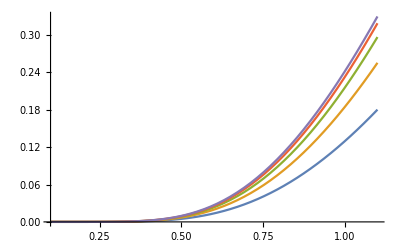

```mathematica
Plot[{Subscript[J, p]/.{κ->1},Subscript[J, p]/.{κ->2},Subscript[J, p]/.{κ->3},Subscript[J, p]/.{κ->4},Subscript[J, p]/.{κ->5}},{T,0.1,1.1}]
```

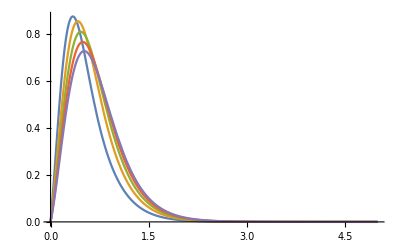

```mathematica
Plot[{Subscript[J, simpu]/.{κ->1},Subscript[J, simpu]/.{κ->2},Subscript[J, simpu]/.{κ->3},Subscript[J, simpu]/.{κ->4},Subscript[J, simpu]/.{κ->5}},{u,0,5}]
```